# Orbigraphs: Defining a Graph Theoretic Analog to Riemannian Orbifolds

## Sam Stewart and Colin Gavin Lewis & Clark College - Portland, OR | -Graphics-

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<"Orbigraphs.m"
```

## Outline

Manifolds to Regular Graphs

Orbifolds to Orbigraphs

Spectral Geometry to Spectral Graph Theory

(Structure stuff)

Further results (time permitting)

## From Manifolds to Regular Graphs (1)

Manifolds: topological spaces that are locally modeled on ℝ^n

Surfaces in ℝ^3 locally look like ℝ^2

Example: S^2

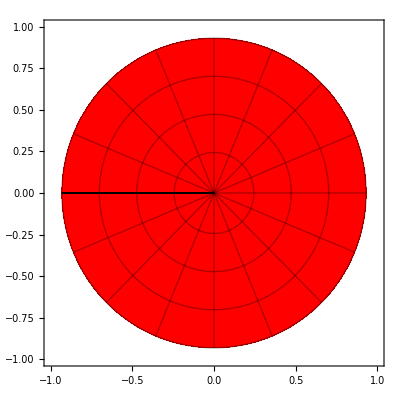
| ⟶ | -Graphics-

```mathematica
s=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,0.5},{θ,0,2π},PlotStyle->Blue,PlotRange->{{-1,1},{-1,1},{-1,1}},Mesh->{9,15}];
c=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,0.5,1},{θ,0,2π},PlotStyle->Red,Mesh->{3,15}];
frames=Table[Show[s,c,SphericalRegion->True,Axes->False,ViewVector->{5 Sin[t],5 Cos[t],2},ImageSize->{200,200}],{t,0,2π,2π/100}];
maniChart=RegionPlot[x^2+y^2≤Sqrt[1-0.5^2],{x,-1,1},{y,-1,1},PlotStyle->Red,Mesh->{3,15},MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100];
{{Dynamic[frames⟦Clock[{1,101,1},10]⟧],"⟶",maniChart}}//Grid
```

## From Manifolds to Regular Graphs (2)

Regular graphs: undirected graphs with constant degree k

Example: 4-regular graphs on 8 vertices

```mathematica
Grid[Partition[SetProperty[#,{ImageSize->120,VertexSize->0.2}]&/@ImportRegularGraphs[8,4],3],Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

Neighborhoods of vertices look like k-stars:

```mathematica
hi={{1},{2,1<->2},{3,1<->3},{4,1<->4},{5,1<->5}};Grid[{{SetProperty[HighlightGraph[ImportRegularGraphs[8,4]⟦3⟧,hi],{VertexSize->0.2}],"⟶",HighlightGraph[StarGraph[5,VertexSize->0.2],hi]}}]
```

-Graphics- | ⟶ | -Graphics-

## From Orbifolds to Orbigraphs (1)

Orbifolds: manifolds with some singular points

Topological spaces locally modeled on ℝ^n/G where G is a finite group of isometries

Appear as a tool in geometry and an object of study on their own

Example: S^2 with a cone point

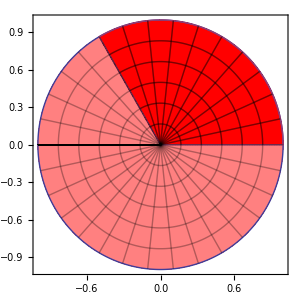
| ⟶ | -Graphics-
ℤ_3 ⟳ D^2

```mathematica
teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];
orbiFrames=Table[Show[cone,bulb,SphericalRegion->True,Axes->False,ViewVector->{10 Sin[t],10 Cos[t],2},ImageSize->{300,300}],{t,0,2π,2π/100}];
orbiChart=Column[{RegionPlot[{x^2+y^2≤1,x^2+y^2≤1&&0≤ArcTan[x,y]≤2π/3},{x,-1,1},{y,-1,1},PlotStyle->{Pink,Red},Mesh->{5,Table[ø,{ø,-π,π,2π/30}]},ImageSize->{300,300},MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100],"ℤ_3 ⟳ D^2"},Center];
{{Dynamic[orbiFrames⟦Clock[{1,101,1},10]⟧],"⟶",orbiChart}}//Grid
```

## From Orbifolds to Orbigraphs (2)

Want to complete the analogy: “___ are to regular graphs as orbifolds are to manifolds”

Neighborhoods: look like quotients of k-stars

```mathematica
multiArrows[adj_,pts_List,e_]:=Module[{bumps,es,normal},
es=adj⟦e⟦1⟧,e⟦2⟧⟧;
If[es<2,Return[Arrow[pts]]];
normal=Cross[pts⟦2⟧-pts⟦1⟧];
bumps=Table[normal*(n 0.6/(es-1)-0.3),{n,0,es-1}];
Arrow[BezierCurve[{pts⟦1⟧,Mean@pts+#,pts⟦2⟧}]]&/@bumps];
s=StarGraph[7,DirectedEdges->True,VertexStyle->{2->Red,3->Red},EdgeStyle->{1->2->Red,1->3->Red},VertexSize->0.1];
orbiStar=OrbigraphFromGroup[s,PermutationGroup[{Cycles[{{2,3}}]}]];
orbiStar=SetProperty[orbiStar,{GraphLayout->"RadialEmbedding",VertexSize->0.1,ImageSize->{200,200},EdgeLabels->None,EdgeShapeFunction->(multiArrows[WeightedAdjacencyMatrix@orbiStar,#1,#2]&)}];
orbiStar=SetProperty[orbiStar,
{VertexStyle->{1->Blue,2->Red,3->Green,4->Yellow,5->Purple,6->Orange},
EdgeStyle->{1->6->Orange,1->2->Red,1->3->Green,1->4->Yellow,1->5->Purple}}];
{{"ℤ_2⟳",s=StarGraph[7,DirectedEdges->True,VertexStyle->{1->Blue,2->Green,3->Yellow,4->Purple,5->Orange,6->Red,7->Red},EdgeStyle->{1->6->Red,1->7->Red,1->2->Green,1->3->Yellow,1->4->Purple,1->5->Orange},VertexSize->0.1],
"⟶",orbiStar
}}//Grid
```

ℤ_2⟳ | -Graphics- | ⟶ | -Graphics-

Compatibility condition: if there is an edge from v_1 to v_2 then there is one from v_2 to v_1

```mathematica
SetProperty[AdjacencyOrbigraph@{{0,2},{1,0}},VertexLabels->{1->Subscript[v, 2],2->Subscript[v, 1]}]
```

-Graphics-

## Orbigraphs

Definition: k-orbigraphs are multi-digraphs with adjacency matrix [a_ij] such that

Entries are integers

Every row sums to k

a_ij≠0 if and only if a_ji≠0

Examples:

```mathematica
Grid[List@Take[DeleteIsomorphicGraphs[Select[AdjacencyOrbigraph/@EnumerateOrbigraphs[3,3],ConnectedGraphQ]],-6],Frame->All]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Spectral Results (1)

Idea: Investigating the resonant frequencies of an object tells us about the geometry

```mathematica
plots=Table[Plot[Evaluate[Sin[k π t]Sin[k π x]/.{k->ks,t->s}],{x,0,1},PlotRange->{{0,1},{-1,1}},ImageSize->{300,200}],{ks,1,3},{s,0,2-0.02,0.02}];
animations=MapIndexed[ListAnimate[#1,Dynamic[If[idx==First@#2,20,0]]]&,plots];
TabView[animations,Dynamic[idx]]
```

123

For graphs, consider the eigenvalues of the adjacency matrix

```mathematica
exGr=CompleteGraph[4,ImageSize->200];
Row[{exGr," ⟶ ",AdjacencyMatrix@exGr//MatrixForm," ⟶ ",Eigenvalues@AdjacencyMatrix@exGr}]
```

-Graphics- ⟶ (0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0) ⟶ {3,-1,-1,-1}

## Spectral Results (2)

Many results about k-regular graphs hold for k-orbigraphs

Spectral radius is k

Bipartite if and only if spectrum is symmetric about zero

Specific results about orbigraphs

Theorem: If Γ is a k-orbigraph on n vertices with spectrum λ_1,…,λ_n and s singular points, then we have:

(∑_i λ_i^2-n k)/(k^2-k)≤s≤∑_i (λ_i^2-n k)

Example:

```mathematica
singularEx=SetProperty[AdjacencyOrbigraph@({{0, 0, 1, 2}, {0, 0, 2, 1}, {1, 1, 1, 0}, {1, 1, 0, 1}}),ImageSize->200];
spec=OrbigraphSpectrum@singularEx;
Row@{singularEx," ⟶ ",Sort[spec,Less]," ⟶ ",(Total[spec^2]-12)/6≤"s"≤Total[spec^2]-12}
```

-Graphics- ⟶ {-2,0,1,3} ⟶ 1/3≤s≤2